# Sampling

## Initialization

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

```mathematica
ExportImages[file_,frames_]:=Block[{indexLength,directory,name},
indexLength = Length[IntegerDigits[Length[frames]]];
directory = DirectoryName[file];
name = FileBaseName[file];

MapIndexed[
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[#2,10,indexLength],".png"]}],
#1
]&,
frames
]
];
```

```mathematica
FillMissing[prices_]:=Block[{propagateBackwards,propagateForward},
propagateBackwards = FixedPoint[
SequenceReplace[#,
{
{"null",x_ /;NumberQ[x]}:>Sequence[x,x],
{None,x_ /;NumberQ[x]}:>Sequence[x,x]
}
]&,
prices
];
propagateForward = FixedPoint[
SequenceReplace[#,
{
{x_ /;NumberQ[x],"null"}:>Sequence[x,x],
{x_ /;NumberQ[x],None}:>Sequence[x,x],
{x_ /;NumberQ[x],""}:>Sequence[x,x]
}
]&,
propagateBackwards
];
Return[propagateForward];
];

ToFinancialData[dataset_]:=Block[{formatted},
formatted = Map[{DateList[First[#]],Rest[#]}&,dataset];
DeleteCases[formatted,{_,{"","","","",""}}]
];
ImportDatabase[date_]:=Block[{files,stocks,dataset},
files = FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV",date}]];
stocks = Map[FileBaseName,files];

Association@Map[FileBaseName[#]->ToFinancialData@Drop[Import[#],1]&,files]
];
```

```mathematica
dateFolders = Select[FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV"}]],FileExtension[#]==""&];
```

```mathematica
dates = Map[FileBaseName,dateFolders]
```

{20-01-2020,21-01-2020,22-01-2020,23-01-2020,24-01-2020,27-01-2020,28-01-2020,29-01-2020}

```mathematica
rawDatabase =ProgressMap[ImportDatabase,dates];
```

```mathematica
database = Merge[rawDatabase,Apply[Join,#]&];
```

```mathematica
database // Keys
```

{AC.MX,ALPEKA.MX,ALSEA.MX,AMXL.MX,ASURB.MX,BBAJIOO.MX,BIMBOA.MX,BOLSAA.MX,BSMXB.MX,CEMEXCPO.MX,CUERVO.MX,GAPB.MX,GCARSOA1.MX,GCC.MX,GENTERA.MX,GFNORTEO.MX,GMEXICOB.MX,GRUMAB.MX,IENOVA.MX,KIMBERA.MX,KOFUBL.MX,LABB.MX,LIVEPOLC-1.MX,MEGACPO.MX,OMAB.MX,ORBIA.MX,PE&OLES.MX,PINFRA.MX,RA.MX,TLEVISACPO.MX}

```mathematica
first = First@database["TLEVISACPO.MX"][[All,2]];
ohlc = Prepend[DeleteCases[database["TLEVISACPO.MX"][[All,2]],{_,_,_,_,0.}],first]
```

{{46.46,46.57,46.46,46.57,0.},{46.88,46.92,46.88,46.92,300.},{46.96,46.96,46.96,46.96,180.},{46.96,46.96,46.96,46.96,300.},2069,{44.55,44.55,44.55,44.55,4810.},{44.56,44.56,44.46,44.51,7110.},{44.51,44.56,44.48,44.48,9213.},{44.47,44.55,44.46,44.54,18891.}}
 |  |  |  |

```mathematica
{volume,closePrices}= {ohlc[[All,5]],ohlc[[All,4]]};
volumePriceInterpolation = Interpolation[Transpose[{Accumulate[volume],closePrices}],InterpolationOrder->1];
pricesSampledByVolume = Table[{vol,volumePriceInterpolation[vol]},{vol,Range[0,Last@Accumulate[volume],20000]}];
```

```mathematica
Length[pricesSampledByVolume]
```

850

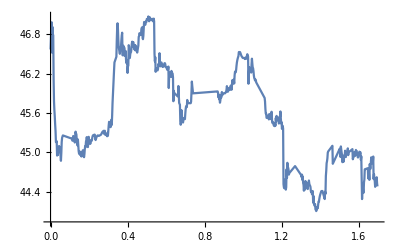

```mathematica
ListLinePlot[pricesSampledByVolume]
```

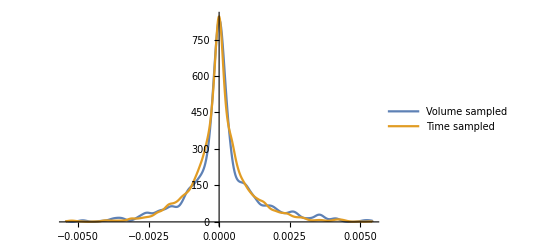

```mathematica
data = Returns[pricesSampledByVolume[[All,2]]];
σ = StandardDeviation[data];
timeSampledReturns = Returns[ohlc[[All,4]]];
SmoothHistogram[{data,timeSampledReturns},PlotRange->{{-3σ,3σ},All},PlotLegends->{"Volume sampled","Time sampled"}]
```

```mathematica
DistributionFitTest[data]
```

0.